```mathematica
<<xAct`xTensor`
<<xAct`xTerior`
<<xAct`xCoba`(*Package*)
```

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xTerior`  version 0.9.1, {2019,5,17}

Copyright (C) 2013-2019, Alfonso Garcia-Parrado Gomez-Lobo and Leo C. Stein, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
Hodge
```

```mathematica
$PrePrint=ScreenDollarIndices;(*Was needed for nice printouts*)$CVVerbose=False;
DefManifold[Omega5,5,{a,b,c,d,e,f,i,j,k,l,m,n,o}];
(*4d manifold called M4,indices to be used*)
```

** DefManifold: Defining manifold Omega5.

** DefVBundle: Defining vbundle TangentOmega5.

```mathematica
DefChart[cart,Omega5,{1,2,3,4,5},{x1[],x2[],x3[],x4[],u[]},ChartColor->Blue]
```

** DefChart: Defining chart cart.

** DefTensor: Defining coordinate scalar x1[].

** DefTensor: Defining coordinate scalar x2[].

** DefTensor: Defining coordinate scalar x3[].

** DefTensor: Defining coordinate scalar x4[].

** DefTensor: Defining coordinate scalar u[].

** DefMapping: Defining mapping cart.

** DefMapping: Defining inverse mapping icart.

** DefTensor: Defining mapping differential tensor dicart[-a,icarta].

** DefTensor: Defining mapping differential tensor dcart[-a,carta].

** DefBasis: Defining basis cart. Coordinated basis.

** DefCovD: Defining parallel derivative PDcart[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDcart[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDcart[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDcart[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDcart[-a,-b].

** DefInertHead: Defining inert head CovDPDcart.

** DefTensor: Defining antisymmetric +1 density etaUpcart[a,b,c,d,e].

** DefTensor: Defining antisymmetric -1 density etaDowncart[-a,-b,-c,-d,-e].

** DefTensor: Defining tensor cart1[].

** DefTensor: Defining tensor cart2[].

** DefTensor: Defining tensor cart3[].

** DefTensor: Defining tensor cart4[].

** DefTensor: Defining tensor cart5[].

```mathematica
DefChart[spherical,Omega5,{1,2,3,4,5},{r[],ϕ1[],ϕ2[],ϕ3[],u[]},ChartColor->Red]
```

** DefChart: Defining chart spherical.

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar ϕ1[].

** DefTensor: Defining coordinate scalar ϕ2[].

** DefTensor: Defining coordinate scalar ϕ3[].

** DefMapping: Defining mapping spherical.

** DefMapping: Defining inverse mapping ispherical.

** DefTensor: Defining mapping differential tensor dispherical[-a,isphericala].

** DefTensor: Defining mapping differential tensor dspherical[-a,sphericala].

** DefBasis: Defining basis spherical. Coordinated basis.

** DefCovD: Defining parallel derivative PDspherical[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDspherical[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDspherical[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDspherical[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDspherical[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpspherical[a,b,c,d,e].

** DefTensor: Defining antisymmetric -1 density etaDownspherical[-a,-b,-c,-d,-e].

```mathematica
{x1[]->r[] Cos[ϕ1[]],x2[]->r[] Sin[ϕ1[]] Cos[ϕ2[]],x3[]->r[] Sin[ϕ1[]] Sin[ϕ2[]]Cos[ϕ3[]],x4[]->r[] Sin[ϕ1[]] Sin[ϕ2[]]Cos[ϕ3[]],u[]->u[]}
```

{x1→Cos[ϕ1] r,x2→Cos[ϕ2] r Sin[ϕ1],x3→Cos[ϕ3] r Sin[ϕ1] Sin[ϕ2],x4→Cos[ϕ3] r Sin[ϕ1] Sin[ϕ2],u→u}

```mathematica
met=CTensor[{{1,0,0,0,-2 x2 ϵ1},{0,1,0,0,2 x1 ϵ1},{0,0,1,0,2 x4 ϵ2},{0,0,0,1,-2 x3 ϵ2},{-2 x2 ϵ1,2 x1 ϵ1,2 x4 ϵ2,-2 x3 ϵ2,1+x1^2 ϵ1^2+x2^2 ϵ1^2+x3^2 ϵ2^2+x4^2 ϵ2^2}},{-cart,-cart}]
```

CTensor[{{1,0,0,0,-2 x2 ϵ1},{0,1,0,0,2 x1 ϵ1},{0,0,1,0,2 x4 ϵ2},{0,0,0,1,-2 x3 ϵ2},{-2 x2 ϵ1,2 x1 ϵ1,2 x4 ϵ2,-2 x3 ϵ2,1+x1^2 ϵ1^2+x2^2 ϵ1^2+x3^2 ϵ2^2+x4^2 ϵ2^2}},{-cart,-cart},0]

```mathematica
met[cart,cart]
```

Hold[Throw[Null]]

```mathematica
{{1,0,0,0,-2 x2 ϵ1},{0,1,0,0,2 x1 ϵ1},{0,0,1,0,2 x4 ϵ2},{0,0,0,1,-2 x3 ϵ2},{-2 x2 ϵ1,2 x1 ϵ1,2 x4 ϵ2,-2 x3 ϵ2,1+x1^2 ϵ1^2+x2^2 ϵ1^2+x3^2 ϵ2^2+x4^2 ϵ2^2}}//MatrixForm
```

(1 | 0 | 0 | 0 | -2 x2 ϵ1
0 | 1 | 0 | 0 | 2 x1 ϵ1
0 | 0 | 1 | 0 | 2 x4 ϵ2
0 | 0 | 0 | 1 | -2 x3 ϵ2
-2 x2 ϵ1 | 2 x1 ϵ1 | 2 x4 ϵ2 | -2 x3 ϵ2 | 1+x1^2 ϵ1^2+x2^2 ϵ1^2+x3^2 ϵ2^2+x4^2 ϵ2^2)

```mathematica
Det[({{1, 0, 0, 0, -2 x2 ϵ1}, {0, 1, 0, 0, 2 x1 ϵ1}, {0, 0, 1, 0, 2 x4 ϵ2}, {0, 0, 0, 1, -2 x3 ϵ2}, {-2 x2 ϵ1, 2 x1 ϵ1, 2 x4 ϵ2, -2 x3 ϵ2, 1+x1^2 ϵ1^2+x2^2 ϵ1^2+x3^2 ϵ2^2+x4^2 ϵ2^2}})]
```

1-3 x1^2 ϵ1^2-3 x2^2 ϵ1^2-3 x3^2 ϵ2^2-3 x4^2 ϵ2^2

```mathematica
-2*(3*e^3*x1^2 + 3*e^3*x3^2 + 3*e^3*x4^2 - e)/(3*e^2*x1^2 + 3*e^2*x2^2 + 3*e^2*x3^2 + 3*e^2*x4^2 - 1)
```

-(2 (-e+3 e^3 x1^2+3 e^3 x3^2+3 e^3 x4^2))/(-1+3 e^2 x1^2+3 e^2 x2^2+3 e^2 x3^2+3 e^2 x4^2)

```mathematica
Apart[-(2 (-e+3 e^3 x1^2+3 e^3 x3^2+3 e^3 x4^2))/(-1+3 e^2 x1^2+3 e^2 x2^2+3 e^2 x3^2+3 e^2 x4^2)]
```

-2 e+(6 e^3 x2^2)/(-1+3 e^2 x1^2+3 e^2 x2^2+3 e^2 x3^2+3 e^2 x4^2)

```mathematica
Simplify[6*e^3*x1*x2/(3*e^2*x1^2+3*e^2*x2^2+3*e^2*x3^2+3*e^2*x4^2-1)]
```

(6 e^3 x1 x2)/(-1+3 e^2 (x1^2+x2^2+x3^2+x4^2))

```mathematica
Corlist={dx1,dx2,dx3,dx4,du};
Table[Coefficient[Coefficient[du^2+dx1^2+dx2^2+dx3^2+dx4^2+2 du dx2 x1 ϵ1-2 du dx1 x2 ϵ1+du^2 x1^2 ϵ1^2+du^2 x2^2 ϵ1^2-2 du dx4 x3 ϵ2+2 du dx3 x4 ϵ2+du^2 x3^2 ϵ2^2+du^2 x4^2 ϵ2^2,cor1,1],cor2,1],{cor1,Corlist},{cor2,Corlist}]+Table[Coefficient[Coefficient[du^2+dx1^2+dx2^2+dx3^2+dx4^2+2 du dx2 x1 ϵ1-2 du dx1 x2 ϵ1+du^2 x1^2 ϵ1^2+du^2 x2^2 ϵ1^2-2 du dx4 x3 ϵ2+2 du dx3 x4 ϵ2+du^2 x3^2 ϵ2^2+du^2 x4^2 ϵ2^2,cor1,2],cor2,2],{cor1,Corlist},{cor2,Corlist}]
```

{{0,0,0,0,-2 x2 ϵ1},{0,0,0,0,2 x1 ϵ1},{0,0,0,0,2 x4 ϵ2},{0,0,0,0,-2 x3 ϵ2},{-2 x2 ϵ1,2 x1 ϵ1,2 x4 ϵ2,-2 x3 ϵ2,0}}

```mathematica
Table[Coefficient[du^2+dx1^2+dx2^2+dx3^2+dx4^2+2 du dx2 x1 ϵ1-2 du dx1 x2 ϵ1+du^2 x1^2 ϵ1^2+du^2 x2^2 ϵ1^2-2 du dx4 x3 ϵ2+2 du dx3 x4 ϵ2+du^2 x3^2 ϵ2^2+du^2 x4^2 ϵ2^2,cor1,2],{cor1,Corlist}]
```

{1,1,1,1,1+x1^2 ϵ1^2+x2^2 ϵ1^2+x3^2 ϵ2^2+x4^2 ϵ2^2}

```mathematica
Map[PDsph[-a],%,{2}]
```

{PDsph[-a][x1]→PDsph[-a][Cos[ϕ1] r],PDsph[-a][x2]→PDsph[-a][Cos[ϕ2] r Sin[ϕ1]],PDsph[-a][x3]→PDsph[-a][Cos[ϕ3] r Sin[ϕ1] Sin[ϕ2]],PDsph[-a][x4]→PDsph[-a][Cos[ϕ3] r Sin[ϕ1] Sin[ϕ2]],PDsph[-a][u]→PDsph[-a][u]}

```mathematica
Reduce[{dx1+I dx2 == dρ1 E^(I ϕ1)+ρ1 E^(I ϕ1)dϕ1,dx3+I dx4 == dρ2 E^(I ϕ2)+ρ2 E^(I ϕ2)dϕ2,x1+I x2 == ρ1 E^(I ϕ1),x3+I x4 == ρ2 E^(I ϕ2)}]
```

((ρ1≠0&&ⅇ^(ⅈ ϕ1)==(x1+ⅈ x2)/ρ1&&dx1==-ⅈ dx2+dρ1 ⅇ^(ⅈ ϕ1)+dϕ1 x1+ⅈ dϕ1 x2)||(ρ1==0&&x1==-ⅈ x2&&dx1==-ⅈ dx2+dρ1 ⅇ^(ⅈ ϕ1)))&&((ρ2≠0&&ⅇ^(ⅈ ϕ2)==(x3+ⅈ x4)/ρ2&&dx3==-ⅈ dx4+dρ2 ⅇ^(ⅈ ϕ2)+dϕ2 x3+ⅈ dϕ2 x4)||(ρ2==0&&x3==-ⅈ x4&&dx3==-ⅈ dx4+dρ2 ⅇ^(ⅈ ϕ2)))

```mathematica
Expand[ (dx1-ϵ1 x2 du)^2+(dx2+ϵ1 x1 du)^2+(dx3+ϵ2 x4 du)^2+(dx4-ϵ2 x3 du)^2+du^2]
```

du^2+dx1^2+dx2^2+dx3^2+dx4^2+2 du dx2 x1 ϵ1-2 du dx1 x2 ϵ1+du^2 x1^2 ϵ1^2+du^2 x2^2 ϵ1^2-2 du dx4 x3 ϵ2+2 du dx3 x4 ϵ2+du^2 x3^2 ϵ2^2+du^2 x4^2 ϵ2^2

```mathematica
Solve[{dx1+I dx2 == dρ1 (x1+I x2)/□ +ρ1 E^(I ϕ1)dϕ1,dx3+I dx4 == dρ2 E^(I ϕ2)+ρ2 E^(I ϕ2)dϕ2,x1+I x2 == ρ1 E^(I ϕ1),x3+I x4 == ρ2 E^(I ϕ2)}]
```

```mathematica
666565666666666666666777777777777
```

```mathematica
Quit[]
```

```mathematica
<<Ricci.m
```

-- Ricci Version 1.61 (March 10, 2016) --

Copyright 1992 - 2016 John M. Lee

Problem reports or suggestions to:

lee@math.washington.edu

-- For properly formatted output in a notebook,

set the default output format type to OutputForm

```mathematica
DefineTensor[F,2,Symmetries->Skew]
```

```mathematica
HodgeDual[]
```

```mathematica
(((4 e^2 Subscript[x, 1] Subscript[x, 2] Subscript[F, 13][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],u]+3 e^2 Subscript[x, 2]^2 Subscript[F, 23][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],u]+3 e^2 Subscript[x, 3]^2 Subscript[F, 23][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],u]-e^2 Subscript[x, 4]^2 Subscript[F, 23][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],u]-4 e^2 Subscript[x, 1] Subscript[x, 3] Subscript[F, 34][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],u]-2 e Subscript[x, 1] Subscript[F, 35][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],u]-2 (2 e^2 Subscript[x, 2] Subscript[F, 12][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],u]-2 e^2 Subscript[x, 3] Subscript[F, 24][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],u]-e Subscript[F, 25][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],u]) Subscript[x, 4]-(e^2 Subscript[x, 1]^2+1) Subscript[F, 23][Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],u]) √(-3 e^2 Subscript[x, 1]^2-3 e^2 Subscript[x, 2]^2-3 e^2 Subscript[x, 3]^2-3 e^2 Subscript[x, 4]^2+1)))/(3 e^2 Subscript[x, 1]^2+3 e^2 Subscript[x, 2]^2+3 e^2 Subscript[x, 3]^2+3 e^2 Subscript[x, 4]^2-1)//Simplify
```

(4 e^2 x_2 (x_4 F_12[x_1,x_2,x_3,x_4,u]-x_1 F_13[x_1,x_2,x_3,x_4,u])-3 e^2 x_2^2 F_23[x_1,x_2,x_3,x_4,u]+(1+e^2 x_1^2-3 e^2 x_3^2+e^2 x_4^2) F_23[x_1,x_2,x_3,x_4,u]+2 e (-x_4 F_25[x_1,x_2,x_3,x_4,u]+x_3 (-2 e x_4 F_24[x_1,x_2,x_3,x_4,u]+2 e x_1 F_34[x_1,x_2,x_3,x_4,u])+x_1 F_35[x_1,x_2,x_3,x_4,u]))/(√(1-3 e^2 x_1^2-3 e^2 x_2^2-3 e^2 x_3^2-3 e^2 x_4^2))

```mathematica
d x1⋀d x2⋀d x3//TensorReduce
```

d^3 x1 x2 x3

```mathematica
Simplify@TensorReduce[(Dt[Subscript[x, 1]]-r Dt[θ] Sin[θ])\[TensorWedge](r Cos[θ] Dt[θ]+Dt[r] Sin[θ])]
```

(-r Dt[θ] Sin[θ]+Dt[x] Subscript^(1,0)[x,1])\[TensorWedge](r Cos[θ] Dt[θ]+Dt[r] Sin[θ])

```mathematica
Simplify@TensorReduce[(Dt[r]-r Dt[θ] Sin[θ])\[TensorWedge](r Cos[θ] Dt[θ]+Dt[r] Sin[θ])]
```

r (Cos[θ]+Sin[θ]^2) Dt[r]\[TensorWedge]Dt[θ]

```mathematica
$Assumptions=r∈Reals&&(Dt[x1]|Dt[x2]|Dt[x3])∈Vectors[{d}]
```

r∈ℝ&&(Dt[x1]|Dt[x2]|Dt[x3])∈Vectors[d,ℂ]

```mathematica
Dt[Subscript[x, 1]]⋀Dt[Subscript[x, 2]]⋀Dt[ Subscript[x, 3]]
```

Dt[x]^3 Subscript^(1,0)[x,1] Subscript^(1,0)[x,2] Subscript^(1,0)[x,3]

```mathematica
$Assumptions=r∈Reals&&(Dt[r]|Dt[θ])∈Vectors[{d}];
Simplify@TensorReduce[TensorWedge[Cos[θ] Dt[r]-r Dt[θ] Sin[θ],r Cos[θ] Dt[θ]+Dt[r] Sin[θ]]]
```

r Dt[r]\[TensorWedge]Dt[θ]

```mathematica
ArcTan[Sin[ϕ]/Cos[ϕ]]//Simplify
```

ArcTan[Tan[ϕ]]

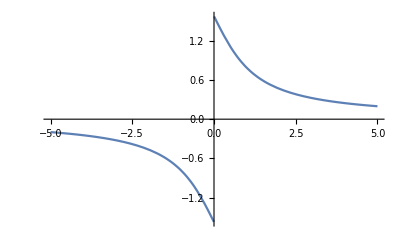

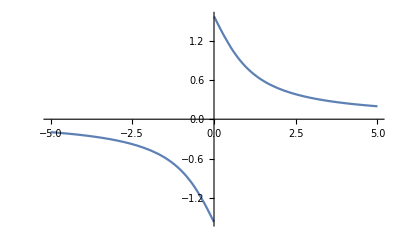

```mathematica
Plot[ArcCot[x],{x,-5,5}]
Plot[ArcTan[1/x],{x,-5,5}]
```

```mathematica
-6*(9*e^4*r^2-4*e^2)/(9*e^4*r^4-6*e^2*r^2+1)//Simplify
```

(6 e^2 (4-9 e^2 r^2))/((1-3 e^2 r^2)^2)

```mathematica
e/.e->4
```

4

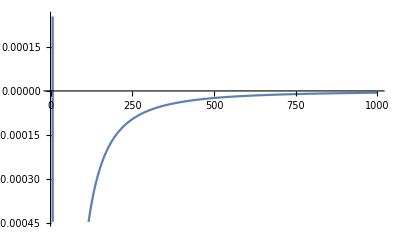

```mathematica
Plot[(6 e^2 (4-9 e^2 r^2))/((1-3 e^2 r^2)^2)/.{e->0.1},{r,0,1000}]
```